```mathematica
data=Import["~/Downloads/pmtk3-master/data/20news_w100.mat"];
```

```mathematica
documents=data⟦1⟧;
```

```mathematica
wordlist=Flatten[FromCharacterCode/@data⟦2⟧];
```

```mathematica
newsgroups=data⟦3⟧;
```

```mathematica
groupnames=Map[FromCharacterCode,data⟦4⟧];
```

```mathematica
nwords=Total[documents];
```

```mathematica
nwords=Total@Values[ArrayRules[#]]&/@(documentsᵀ);
```

```mathematica
x=documents⟦;;,Ordering[nwords,-1000]⟧;
```

```mathematica
y=Flatten[newsgroups⟦;;,Ordering[nwords,-1000]⟧];
```

```mathematica
x=Normal[x]⟦;;,Ordering[y]⟧;
```

```mathematica
y=y⟦Ordering[y]⟧;
```

```mathematica
lines=Line[{{0,Length@y-#},{100,Length@y-#}}]&/@Flatten[FirstPosition[y,#]&/@{2.,3.,4.}];
```

```mathematica
ArrayPlot[xᵀ,Epilog->{Directive[{Thick,Red}],lines},AspectRatio->1]
```

-Graphics-

```mathematica
sample=x⟦;;,Flatten@RandomSample[Position[ y,1.],3]⟧;
```

```mathematica
wordlist[[Take[Flatten@Keys[ArrayRules[sample[[;;,#]]]],{1,-2}]]]&/@Range[3]
```

{{computer,email,fact,ftp,help,memory,program,science,server,university,version},{case,data,display,dos,human,image,number,pc,space,system,video},{case,dos,graphics,law,number,pc,phone,problem,software,university}}

```mathematica
sample=x⟦;;,Flatten@RandomSample[Position[ y,2.],3]⟧;
```

```mathematica
wordlist[[Take[Flatten@Keys[ArrayRules[sample[[;;,#]]]],{1,-2}]]]&/@Range[3]
```

{{case,computer,course,hockey,jesus,league,players,puck,science,team,university},{baseball,course,doctor,games,help,players,problem,religion,season,win,world},{case,course,fans,games,hockey,league,nhl,number,players,question,system}}

```mathematica
sample=x⟦;;,Flatten@RandomSample[Position[ y,3.],3]⟧;
```

```mathematica
wordlist[[Take[Flatten@Keys[ArrayRules[sample[[;;,#]]]],{1,-2}]]]&/@Range[3]
```

{{card,computer,data,driver,earth,email,engine,files,ftp,government,launch,league,lunar,mars,mission,moon,nasa,number,orbit,pc,phone,power,program,research,satellite,science,server,shuttle,software,solar,space,state,studies,system,technology,university},{baseball,data,food,human,orbit,problem,program,research,science,space,technology,world},{case,computer,drive,fact,image,mission,shuttle,software,space,system,technology}}

```mathematica
sample=x⟦;;,Flatten@RandomSample[Position[ y,4.],3]⟧;
```

```mathematica
wordlist[[Take[Flatten@Keys[ArrayRules[sample[[;;,#]]]],{1,-2}]]]&/@Range[3]
```

{{christian,course,fact,god,help,power,religion,state,version,world},{bible,case,children,christian,god,image,jesus,jews,number,question,religion,water},{bible,children,christian,evidence,fact,god,human,law,program,rights,water}}

```mathematica
data=ExampleData[{"Statistics","FisherIris"}];
```

```mathematica
labels=DeleteDuplicates[Part[#,5]&/@data]
```

{setosa,versicolor,virginica}

```mathematica
idx=Flatten@Position[data⟦All,5⟧,#]&/@labels;
```

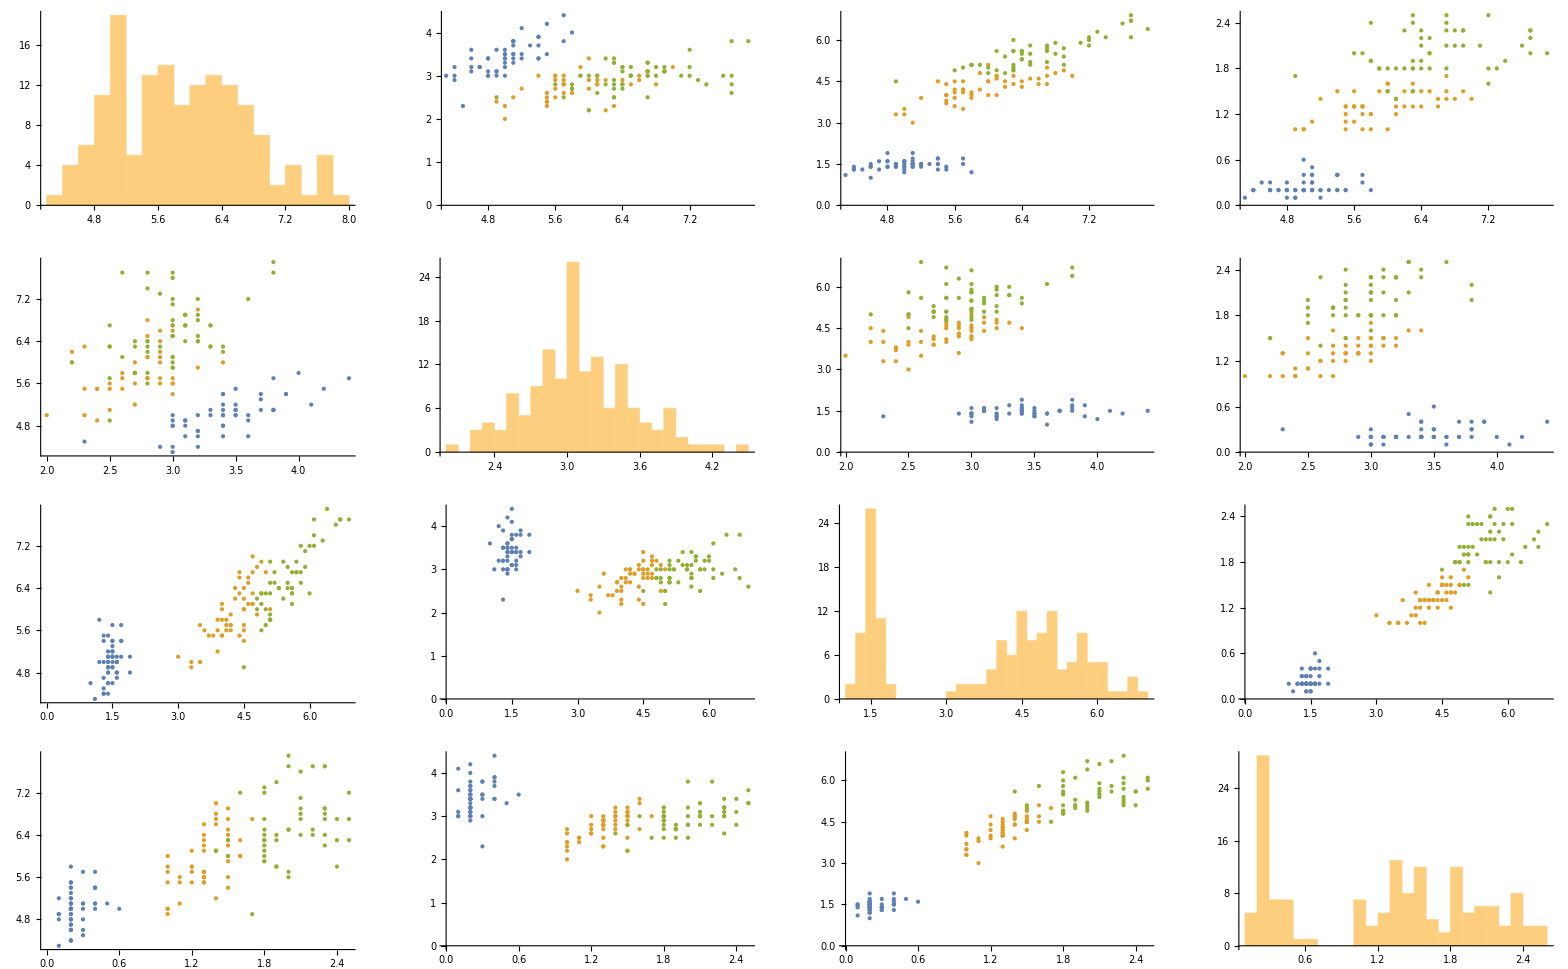

```mathematica
GraphicsGrid[Table[If[i==j,Histogram[data⟦All,i⟧,20,ImagePadding->0],ListPlot[data⟦#,{i,j}⟧&/@idx,ImagePadding->0,PlotStyle-> PointSize[Medium]]],{i,1,4},{j,1,4}]]
```

```mathematica
data=Import["~/Downloads/pmtk3-master/data/heightWeight/heightWeight.mat"]⟦1⟧;
```

```mathematica
prevErr=Infinity;
```

```mathematica
x=data⟦All,2;;3⟧;y=data⟦All,1⟧;
```

```mathematica
mu=RandomSample[x,3];
```

```mathematica
distMatrix[p_,q_,pss_:Null,qss_:Null]:=
Module[{
ps=If[pss==Null,Total[Power[p,2],{2}],pss],qs=If[qss==Null,Total[Power[q,2],{2}], qss]},
Sqrt[Outer[Plus,ps,qs]-2*p.qᵀ]]
```

```mathematica
kMeans[x_,k_]:=
Module[{prevErr=Infinity,mu=RandomSample[x,k],converged=False,dists,assign,newMu,err},
While[Not[converged],
dists=distMatrix[x,mu];
assign=Flatten[First@Position[#,Min[#]]&/@dists];
newMu=Mean[x⟦Flatten@Position[assign,#]⟧]&/@Sort@DeleteDuplicates@assign;
err=Total@MapThread[#1⟦#2⟧&,{dists,assign}]/Length@x;
converged=If[prevErr==Infinity,False,Abs[err-prevErr]/((Abs[err]+Abs[prevErr])/2)<1.×10^-4];
mu=newMu;
prevErr=err;];
{mu,err,assign}]
```

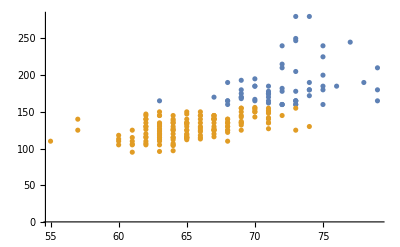

```mathematica
k=2;clusters=kMeans[x,k]⟦3⟧;ListPlot[x⟦Flatten@Position[clusters,#]⟧&/@Table[i,{i,1,k}]]
```

```mathematica
n=100;d=3;
```

```mathematica
mu=ConstantArray[0,d];sigma=DiagonalMatrix[Sqrt@{10,2,0.5}];
```

```mathematica
a=CholeskyDecomposition[sigma];
```

```mathematica
z=RandomVariate[NormalDistribution[],{d,n}];
```

```mathematica
x=#+mu&/@((a.z)ᵀ);
```

```mathematica
alpha=30/180*π;
```

```mathematica
r=({{Cos[alpha], -Sin[alpha], 0}, {Sin[alpha], Cos[alpha], 0}, {0, 0, 1}});
```

```mathematica
x=x.rᵀ;
```

```mathematica
ListPointPlot3D[x]
```

-Graphics3D-

```mathematica
c=Mean[x];x=(#-c&/@x);
```

```mathematica
{vals,u}=Eigensystem[x.xᵀ];u=uᵀ;
```

```mathematica
w=Re[(xᵀ.u).DiagonalMatrix[1/Sqrt[vals]]];w=w⟦All,1;;2⟧;
```

```mathematica
z=x.w;
```

```mathematica
xRecon2=#+c&/@(z.wᵀ);
```

```mathematica
xRecon1=c+#&/@Outer[Times,z⟦All,1⟧,w⟦All,1⟧];
```

```mathematica
x=#+c&/@x;
```

```mathematica
Show[
ListPointPlot3D[x],
Graphics3D[{Red,Line[{10*w⟦All,1⟧,-10*w⟦All,1⟧}]}],Graphics3D[{Red,Dashed,Line[{10*w⟦All,2⟧,-10*w⟦All,2⟧}]}]]
```

-Graphics3D-

```mathematica
Show@Join[{ListPointPlot3D[x]},MapThread[Graphics3D[Line[{#1,#2}]]&,{x,xRecon2}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[xRecon2]
```

-Graphics3D-

```mathematica
ListPointPlot3D[xRecon1]
```

-Graphics3D-

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"olivettifaces.mat"}]];
```

```mathematica
x=data⟦1⟧ᵀ;
```

```mathematica
mu=Mean[x];xc=#-mu&/@x;
```

```mathematica
k=MatrixRank[x];
```

```mathematica
{vals,u}=Eigensystem[x.xᵀ];u=uᵀ;
```

```mathematica
v=Re[(xᵀ.u).DiagonalMatrix[1/Sqrt[vals]]];v=v⟦All,1;;k⟧;
```

```mathematica
z=x.v;
```

```mathematica
Image[ArrayReshape[mu/255,{64,64}]ᵀ]
```

-Graphics-

```mathematica
Table[Image[ArrayReshape[(v⟦All,i⟧+Abs[Min[v⟦All,i⟧]])/(Max[v⟦All,i⟧]-Min[v⟦All,i⟧]),{64,64}]ᵀ],{i,1,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Image[ArrayReshape[(z⟦125,1;;i⟧.v⟦All,1;;i⟧ᵀ)/255,{64,64}]ᵀ],{i,{5,10,20,k}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image[ArrayReshape[x⟦125⟧/255,{64,64}]ᵀ]
```

-Graphics-

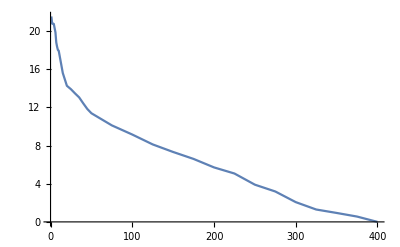

```mathematica
ListLinePlot@Table[{i,Sqrt@Mean[((z⟦125,1;;i⟧.v⟦All,1;;i⟧ᵀ)-x⟦125⟧)^2]},{i,{1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,45,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400}}]
```

```mathematica
ESLII Algorithm 17.1 Modified regression algorithm for estimation of an undirected gaussian graphical model with known structure.
```

```mathematica
step[s_,t_,i_]:=
Module[{w11=Drop[s,{i},{i}],w12=Drop[s⟦i,All⟧,{i}],gIndex=Flatten@Position[Drop[t⟦i,All⟧,{i}],1],otherIndex,w11star,w12star,beta,betastar,p=Dimensions[s]⟦1⟧},
otherIndex=Delete[Range[p-1],gIndex⟦1⟧];
w11star=Drop[w11,gIndex,gIndex];
w12star=Drop[w12,gIndex];
betastar=Inverse[w11star].w12star//N; (* solve Wstar11.betastar - sstar12 = 0 *)
beta=ConstantArray[0,{p-1}];
beta⟦otherIndex⟧=betastar;
beta]
```

```mathematica
iteration[s_,t_]:=
Module[{p=Dimensions[s]⟦1⟧,beta,w12,idx,w=s,theta12,theta22,theta,i},
(* calculate big theta every iteration instead of only the last *)
theta=ConstantArray[0,{p,p}];
For[i=1,i≤p,i++,
beta=step[w,t,i];
w12=Drop[w,{i},{i}].beta;
theta22=1/(s⟦i,i⟧-w12.beta);
theta12=-beta*theta22;
idx=Delete[Range[p],i];
w⟦i,idx⟧=w12;
w⟦idx,i⟧=w12;
theta⟦i,i⟧=theta22;
theta⟦i,idx⟧=theta12;
theta⟦idx,i⟧=theta12];{w,theta}]
```

```mathematica
Example data from book. t matrix encodes node independence.
```

```mathematica
s=({{10, 1, 5, 4}, {1, 10, 2, 6}, {5, 2, 10, 3}, {4, 6, 3, 10}});t=({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}});
```

```mathematica
w=s;iter=1;err=Infinity;
While[err>10^-4&&iter≤10,
{wNew,theta}=iteration[w,t];
err=Total[Abs[wNew-w]^2,2]/Apply[Times,Dimensions[w]];
w=wNew;
iter+=1;]
```

```mathematica
w//MatrixForm
```

(10 | 1. | 1.31421 | 4.
1. | 10 | 2. | 0.870472
1.31421 | 2. | 10 | 3.
4. | 0.870472 | 3. | 10)

```mathematica
theta//MatrixForm
```

(0.119657 | -0.00785898 | 0. | -0.0471789
-0.00785898 | 0.10477 | -0.0199212 | 0.
0. | -0.0199212 | 0.113697 | -0.0323749
-0.0471789 | 0. | -0.0323749 | 0.128584)

```mathematica
S[x_,t_]:=
Sign[x]*If[Positive[Abs[x]-t],Abs[x]-t,0]
```

```mathematica
coordescStep[w11_,w12_,beta_,lambda_]:=
Module[{p=Dimensions[w11]⟦1⟧,idx,newBeta=beta,i},
For[i=1,i≤p,i++,
idx=Delete[Range[p],i];
newBeta⟦i⟧=S[w12⟦i⟧-w11⟦idx,i⟧.newBeta⟦idx⟧//N,lambda]/w11⟦i,i⟧];
newBeta]
```

```mathematica
coordescIter[w11_,w12_,lambda_]:=
Module[{p=Dimensions[w11]⟦1⟧,beta,newBeta,iter=1,err=Infinity},
beta=ConstantArray[0,p];
While[err>10^-4&&iter≤100,
newBeta=coordescStep[w11,w12,beta,lambda];
err=Total[Abs[beta-newBeta]^2]/p//N;
beta=newBeta;
iter+=1;];
beta]
```

```mathematica
graphLassoIter[w_,lambda_]:=
Module[{p=Dimensions[w]⟦1⟧,innerW=w,beta,idx,theta,i},
theta=ConstantArray[0,{p,p}];
For[i=1,i≤p,i++,
Module[{w11=Drop[innerW,{i},{i}],w12=Drop[innerW⟦i,All⟧,{i}],theta22,theta12},
beta=coordescIter[w11,w12,lambda];
w12=w11.beta;
theta22=1/(innerW⟦i,i⟧-w12.beta)//N;
theta12=-beta*theta22;
idx=Delete[Range[p],i];
innerW⟦i,idx⟧=w12;
innerW⟦idx,i⟧=w12;
theta⟦i,i⟧=theta22;
theta⟦i,idx⟧=theta12;
theta⟦idx,i⟧=theta12;]];
{innerW,theta}]
```

```mathematica
graphLasso[w_,lambda_]:=
Module[{iter=1,err=Infinity,lastErr=Infinity,innerW=w,newW,p=Dimensions[w]⟦1⟧,theta,newTheta},
theta=ConstantArray[Infinity,{p,p}];
While[err>10^-4&&iter≤20,
{newW,newTheta}=graphLassoIter[innerW,lambda];
err=Total[Abs[newW-innerW]^2,2]/(p*p)//N;
innerW=newW;
theta=newTheta;
Print[{iter,err,Norm[innerW,1],Norm[theta,1]}];
iter+=1;
If[err-lastErr>10,Print["Error increasing"];Break[]];
lastErr=err;];
{innerW,theta}]
```

```mathematica
data=Import["~/Downloads/pmtk3-master/data/sachsCtsHtf/sachsCtsHtf.mat"];
x=data⟦1⟧;names=data⟦2⟧⟦1⟧;
c=Mean[x];v=StandardDeviation[x]; xc=(#-c)/v&/@x;
s=(xcᵀ.xc)/Length[x];
```

```mathematica
lambda=.008;{ww,tt}=graphLasso[s+lambda*IdentityMatrix[Dimensions[s]⟦1⟧],lambda];
```

{1,0.00015316,4.62924,35.5238}

{2,0.000150704,4.59072,23.1535}

{3,0.0001653,4.50933,19.7163}

{4,0.000159781,4.43177,17.7462}

{5,0.000159875,4.35639,16.0412}

{6,0.000155515,4.2709,15.1266}

{7,0.000150757,4.18022,13.9985}

{8,0.000155932,4.08008,12.8811}

{9,0.000170634,3.96646,11.8324}

{10,0.000164644,3.8499,10.8688}

{11,0.000152074,3.73218,10.0104}

{12,0.000143257,3.61572,9.28875}

{13,0.000135647,3.49874,8.84867}

{14,0.000120255,3.39718,8.37224}

{15,0.000113942,3.29696,7.89424}

{16,0.00010997,3.19767,7.43282}

{17,0.000101346,3.10087,6.99452}

{18,0.0000886502,3.00606,6.57845}

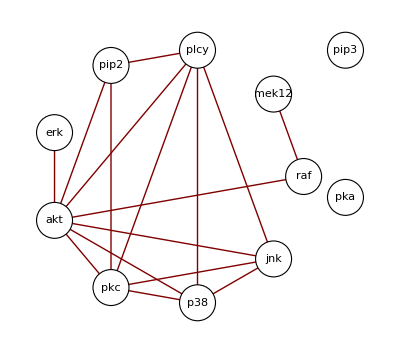

```mathematica
GraphPlot[Map[If[#==0,0,1]&,tt,{2}],VertexLabeling->True,PackingMethod->"Layered",VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.1],Black,Text[names[[#2]],#1]}&),Method->"CircularEmbedding"]
```

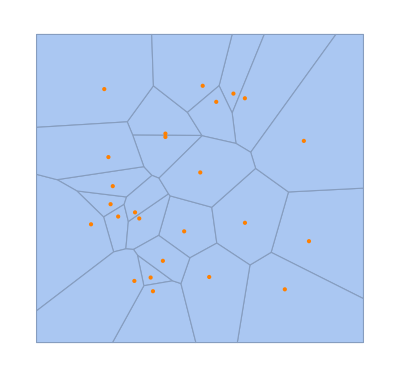

```mathematica
pts=RandomReal[{-1,1},{25,2}];Show[VoronoiMesh@pts,Graphics[{Orange,Point[pts]}]]
```